Si può automatizzare la ricerca della biforcazione. Per determinare la biforcazione n-esima, si parte da un appropriato valore di μ inferiore a quello di biforcazione (stimato ad occhio) e si confrontano, per un N opportunamente grande, le iterate N-esima e (N+2^n)-esima di uno stesso punto inziale. Se sono molto vicini, non siamo ancora alla biforcazione, e bisogna aumentare μ. Appena cominciano ad allontanarsi, siamo arrivati alla biforcazione.

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[μ_,x_]:= μ x(1-x)
fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n]
dist[μ_,x0_,Ν_,n_]:=Abs[10^8 fn[μ,x0,Ν]-10^8 fn[μ,x0,Ν+2^n]]/10^8
indagine[n_,x0_,{min_,max_,step_}]:=ParallelTable[{μ,dist[μ,x0,10^4,n]},{μ,min,max,step}]
```

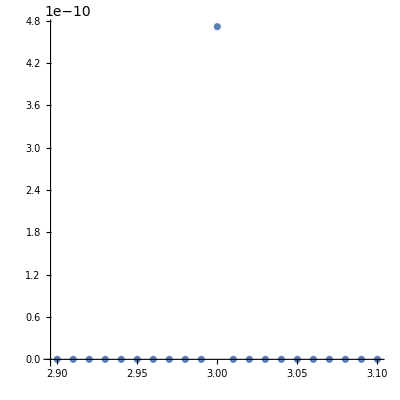

```mathematica
ListPlot[indagine[2,0.4,{2.9,3.1,10^-2}],AspectRatio->1]
```

```mathematica
Module[
{
ind=indagine[2,{2.99,3.01,10^-3}],
val,
spike
},
val=Last/@ind;
spike=Max@val;
Cases[ind,{_,spike}]
]
```

{{3.,4.71716×10^-10}}

```mathematica
Module[
{
ind=indagine[3,0.3,{3.4,3.5,10^-3}],
val,
spike
},
val=Last/@ind;
spike=Max@val;
Cases[ind,{_,spike}]
]
```

{{3.449,3.36636×10^-10}}